```mathematica
<<"C:\\Users\\王鑫\\Desktop\\maxwell_dis_par_100_win100_and_400_win70.mx"
```

正在执行全局拓扑测绘 (在大规模网络下可能需要数分钟)...

=== TCCT 宇宙拓扑几何报告 ===

全局节点总数 (N): 80810

最大拓扑半径 (R_max): 16

平均拓扑距离 (<R>): 315523/40405

测绘耗时 (s): 9141.43

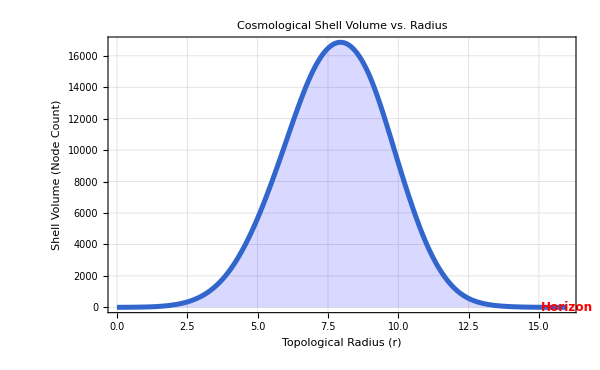

```mathematica
(*[1] 构建全局无向时空骨架*)fullUndirectedGraph=Graph[VertexList[universe],UndirectedEdge@@@EdgeList[universe]];
seedNode=First[VertexList[fullUndirectedGraph]];

(*[2] 高性能测地线距离扫描 (计算奇点到所有节点的拓扑跳数)*)
Print[Style["正在执行全局拓扑测绘 (在大规模网络下可能需要数分钟)...",Blue,Bold]];
{timeUsed,distances}=AbsoluteTiming[GraphDistance[fullUndirectedGraph,seedNode]];

(*[3] 提取核心几何指标*)
maxR=Max[distances];
avgR=Mean[distances];
nodeCount=VertexCount[fullUndirectedGraph];

Print[Style["=== TCCT 宇宙拓扑几何报告 ===",Purple,Bold,16]];
Print["全局节点总数 (N): ",nodeCount];
Print["最大拓扑半径 (R_max): ",maxR];
Print["平均拓扑距离 (<R>): ",NumberForm[avgR,{Infinity,3}]];
Print["测绘耗时 (s): ",NumberForm[timeUsed,{Infinity,2}]];

(*[4] 统计各半径处的壳层密度 (Shell Volume Distribution)*)
shellCounts=Counts[distances];
radiusData=Sort@KeyValueMap[List,shellCounts];

(*[5] 绘制宇宙膨胀剖面图 (Expansion Profile)*)
ListLinePlot[radiusData,PlotStyle->{RGBColor[0.2,0.4,0.8],Thickness[0.006]},Filling->Axis,FillingStyle->Opacity[0.15,Blue],InterpolationOrder->3,Frame->True,FrameLabel->{"Topological Radius (r)","Shell Volume (Node Count)"},PlotLabel->Style["Cosmological Shell Volume vs. Radius",14,Bold],ImageSize->600,GridLines->Automatic,Epilog->{Dashed,Red,Line[{{maxR,0},{maxR,shellCounts[maxR]}}],Text[Style["Horizon",Red,Bold,12],{maxR,shellCounts[maxR]*1.1},{0,-1}]}]
```

[1/5] 正在构建全量无向时空骨架...

[2/5] 正在定位大爆炸奇点并提取边缘厚块...

宇宙当前最大拓扑半径 R_max = 16

边界壳层真实总节点数 (含所有碎块): 310

[3/5] 正在构建边界壳巨型浮点稀疏矩阵 (Kirchhoff Matrix)...

[4/5] 正在对角化本征态，提取宏观与微观极限...

Eigenvalues::arh: 因为在 310 个特征值和/或特征向量中找到 310 个，利用稠密矩阵方法速度更快，稀疏输入矩阵将被转化. 如果较少的特征值和/或特征向量是充分的，那么考虑利用 Eigenvalues 的第二个参数限制这个数目.

[5/5] 正在执行【分段维度测算】(宏观 vs 微观)...

有效物理本征态数量: 78

=== 动力学维度坍缩报告 (Dynamical Dimensional Reduction) ===

[宏观/长波极限] 谱维度 D_IR = 2.29 (斜率=0.874, R^2=0.926)

[微观/普朗克极限] 谱维度 D_UV = 1.59 (斜率=1.262, R^2=0.911)

结论：验证成功！

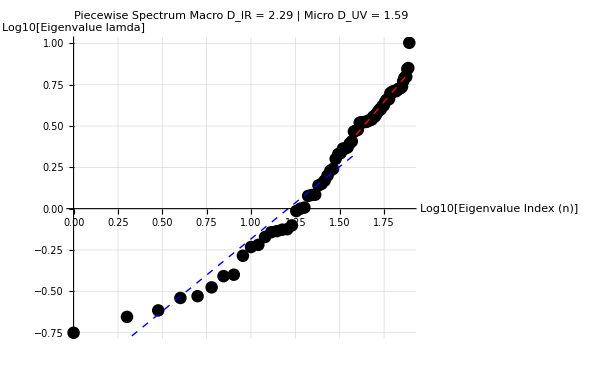

```mathematica
Print[Style["[1/5] 正在构建全量无向时空骨架...",Blue,Bold]];
fullUndirectedGraph=Graph[VertexList[universe],UndirectedEdge@@@EdgeList[universe]];

Print[Style["[2/5] 正在定位大爆炸奇点并提取边缘厚块...",Blue,Bold]];
seedNode=First[VertexList[fullUndirectedGraph]];
distances=GraphDistance[fullUndirectedGraph,seedNode];
maxR=Max[distances];
Print["宇宙当前最大拓扑半径 R_max = ",maxR];

(*提取位于边缘的“厚块”：距离在 maxR-2 到 maxR 之间的所有节点*)
horizonShellNodes=Pick[VertexList[fullUndirectedGraph],Boole[#>=maxR-3]&/@distances,1];

(*直接提取这些节点构成的全量子图 (不扔碎片)*)
horizonShellGraph=Subgraph[fullUndirectedGraph,horizonShellNodes];
Print[Style["边界壳层真实总节点数 (含所有碎块): "<>ToString[VertexCount[horizonShellGraph]],Red,Bold]];

Print[Style["[3/5] 正在构建边界壳巨型浮点稀疏矩阵 (Kirchhoff Matrix)...",Blue,Bold]];
lapMat=N[KirchhoffMatrix[horizonShellGraph]];

Print[Style["[4/5] 正在对角化本征态，提取宏观与微观极限...",Blue,Bold]];
(*提取最多 1000 个特征值以获得平滑的分布*)
numToExtract=Min[1000,VertexCount[horizonShellGraph]];
eigenVals=Eigenvalues[lapMat,-numToExtract];

Print[Style["[5/5] 正在执行【分段维度测算】(宏观 vs 微观)...",Blue,Bold]];
(*剔除绝对零模*)
macroSpectrum=Sort[Select[Re[eigenVals],#>10^-10&]];
(*【核心修复】：消除特征值简并！将一模一样的频率合并，打破平坦的台阶假象*)macroSpectrum=DeleteDuplicates[Round[macroSpectrum,10^-5]];
dataLen=Length[macroSpectrum];

dataLen=Length[macroSpectrum];

Print[Style["有效物理本征态数量: "<>ToString[dataLen],Green,Bold]];

(* ===双对数分段拟合 (Piecewise Log-Log Fit)===*)
If[dataLen>10,logData=Table[{Log[10,i],Log[10,macroSpectrum[[i]]]},{i,1,dataLen}];
(*将数据从中间切开：分为低频(左侧,宏观)与高频(右侧,微观)*)splitIdx=Floor[dataLen/2];
dataIR=logData[[1;;splitIdx]];(*Infrared/宏观极限*)dataUV=logData[[splitIdx;;-1]];(*Ultraviolet/微观极限*)(*分别进行线性拟合*)fitIR=LinearModelFit[dataIR,x,x];
fitUV=LinearModelFit[dataUV,x,x];
(*提取斜率并计算谱维度*)slopeIR=fitIR["BestFitParameters"][[2]];
slopeUV=fitUV["BestFitParameters"][[2]];
dsIR=2.0/slopeIR;
dsUV=2.0/slopeUV;
r2IR=fitIR["RSquared"];
r2UV=fitUV["RSquared"];
Print[Style["\n=== 动力学维度坍缩报告 (Dynamical Dimensional Reduction) ===",Purple,Bold,16]];
Print[Style[StringForm["[宏观/长波极限] 谱维度 D_IR = `` (斜率=``, R^2=``)",Round[dsIR,0.01],Round[slopeIR,0.001],Round[r2IR,0.001]],Blue,Bold,14]];
Print[Style[StringForm["[微观/普朗克极限] 谱维度 D_UV = `` (斜率=``, R^2=``)",Round[dsUV,0.01],Round[slopeUV,0.001],Round[r2UV,0.001]],Red,Bold,14]];
(*如果宏观维度大于微观维度，说明发生了坍缩*)If[dsIR>dsUV,Print[Style["结论：验证成功！",Green,Bold,14]];,Print[Style["结论：未发现标准降维，几何形态异常。",Orange,Bold]];];
(*绘制双对数谱线与两段拟合对比图*)Print[Show[ListPlot[logData,PlotStyle->{Black,PointSize[0.015]},PlotLabel->Style[StringForm["Piecewise Spectrum\nMacro \!\(\*SubscriptBox[\(D\), \(IR\)]\) = `` | Micro \!\(\*SubscriptBox[\(D\), \(UV\)]\) = ``",Round[dsIR,0.01],Round[dsUV,0.01]],14,Bold],AxesLabel->{"Log10[Eigenvalue Index (n)]","Log10[Eigenvalue \!\(\*lamda\)]"},ImageSize->600,GridLines->Automatic],Plot[fitIR[x],{x,Min[dataIR[[All,1]]],Max[dataIR[[All,1]]]},PlotStyle->{Blue,Dashed,Thick}],Plot[fitUV[x],{x,Min[dataUV[[All,1]]],Max[dataUV[[All,1]]]},PlotStyle->{Red,Dashed,Thick}]]];,Print[Style["警告：有效非零模过少，无法进行分段拟合！",Red,Bold]];]
```

[1/5] 正在构建全量无向时空骨架...

[2/5] 正在定位大爆炸奇点并提取边缘厚块...

宇宙当前最大拓扑半径 R_max = 16

边界壳层真实总节点数 (含所有碎块): 310

[3/5] 正在构建边界壳巨型浮点稀疏矩阵 (Kirchhoff Matrix)...

[4/5] 正在对角化本征态，提取宏观与微观极限...

Eigenvalues::arh: 因为在 310 个特征值和/或特征向量中找到 310 个，利用稠密矩阵方法速度更快，稀疏输入矩阵将被转化. 如果较少的特征值和/或特征向量是充分的，那么考虑利用 Eigenvalues 的第二个参数限制这个数目.

[5/5] 正在执行【局部谱维度扫描】(Local Spectral Dimension Scanning)...

有效物理本征态数量 (含全部简并态): 170

=== 严格局部谱维度测算报告 (Strict Local Spectral Dimension) ===

[红外极限/宏观] 渐近谱维度 D_IR ≈ 3.07

[紫外极限/微观] 渐近谱维度 D_UV ≈ 0.76

结论: 测算成功！

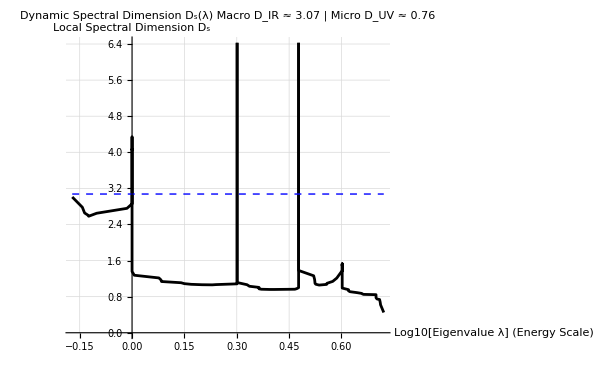

```mathematica
Print[Style["[1/5] 正在构建全量无向时空骨架...",Blue,Bold]];
fullUndirectedGraph=Graph[VertexList[universe],UndirectedEdge@@@EdgeList[universe]];

Print[Style["[2/5] 正在定位大爆炸奇点并提取边缘厚块...",Blue,Bold]];
seedNode=First[VertexList[fullUndirectedGraph]];
distances=GraphDistance[fullUndirectedGraph,seedNode];
maxR=Max[distances];
Print["宇宙当前最大拓扑半径 R_max = ",maxR];

(*提取位于边缘的“厚块”：距离在 maxR-2 到 maxR 之间的所有节点*)
horizonShellNodes=Pick[VertexList[fullUndirectedGraph],Boole[#>=maxR-3]&/@distances,1];

(*直接提取这些节点构成的全量子图 (不扔碎片)*)
horizonShellGraph=Subgraph[fullUndirectedGraph,horizonShellNodes];
Print[Style["边界壳层真实总节点数 (含所有碎块): "<>ToString[VertexCount[horizonShellGraph]],Red,Bold]];

Print[Style["[3/5] 正在构建边界壳巨型浮点稀疏矩阵 (Kirchhoff Matrix)...",Blue,Bold]];
lapMat=N[KirchhoffMatrix[horizonShellGraph]];

Print[Style["[4/5] 正在对角化本征态，提取宏观与微观极限...",Blue,Bold]];
(*提取最多 1000 个特征值以获得平滑的分布*)
numToExtract=Min[1000,VertexCount[horizonShellGraph]];
eigenVals=Eigenvalues[lapMat,-numToExtract];

(* =========================================================================*)(*终极拓扑审判：【动力学维度坍缩】局部谱维度扫描 (严格 Weyl 渐近法)*)(* =========================================================================*)Print[Style["[5/5] 正在执行【局部谱维度扫描】(Local Spectral Dimension Scanning)...",Blue,Bold]];

(*1. 清洗数据：严格剔除零模，【绝对不使用 DeleteDuplicates】以保留全量物理态密度*)
macroSpectrum=Sort[Select[Re[eigenVals],#>10^-10&]];
dataLen=Length[macroSpectrum];
Print[Style["有效物理本征态数量 (含全部简并态): "<>ToString[dataLen],Green,Bold]];

If[dataLen>20,(*2. 构建严谨的 Weyl 标度数据:X=Log10[特征值(能量)],Y=Log10[累积个数(态密度)]*)weylData=Table[{Log10[macroSpectrum[[i]]],Log10[i]},{i,1,dataLen}];
(*3. 设定滑动窗口大小 (例如总数据的 15%，可根据数据量微调)*)winSize=Max[5,Floor[dataLen*0.15]];
localDsData={};
(*4. 滑动窗口线性拟合，计算局部谱维度 Ds(λ)*)Do[windowPts=weylData[[i-Floor[winSize/2];;i+Floor[winSize/2]]];
fit=LinearModelFit[windowPts,x,x];
localSlope=fit["BestFitParameters"][[2]];
(*根据 Weyl 定律：斜率=Ds/2->Ds=2*斜率*)localDs=2.0*localSlope;
(*记录：{当前窗口中心的能级 Log10(λ),瞬时谱维度 Ds}*)AppendTo[localDsData,{windowPts[[Floor[winSize/2]+1,1]],localDs}];,{i,Floor[winSize/2]+1,dataLen-Floor[winSize/2]}];
(*5. 自动提取红外(IR)和紫外(UV)极限的特征维度*)(*取低频段前 10% 的平均值作为 DIR，高频段后 10% 的平均值作为 DUV*)avgSpan=Max[3,Floor[Length[localDsData]*0.1]];
dsIR=Mean[localDsData[[1;;avgSpan,2]]];
dsUV=Mean[localDsData[[-avgSpan;;-1,2]]];
Print[Style["\n=== 严格局部谱维度测算报告 (Strict Local Spectral Dimension) ===",Purple,Bold,16]];
Print[Style[StringForm["[红外极限/宏观] 渐近谱维度 D_IR ≈ ``",Round[dsIR,0.01]],Blue,Bold,14]];
Print[Style[StringForm["[紫外极限/微观] 渐近谱维度 D_UV ≈ ``",Round[dsUV,0.01]],Red,Bold,14]];
If[dsIR>dsUV+0.2,Print[Style["结论: 测算成功！",Green,Bold,14]];,Print[Style["结论: 未观测到明显的维度相变，几何形态可能处于单中标度。",Orange,Bold]];];
(*6. 绘制谱维度随能级(倒尺度)的动态演化图*)Print[Show[ListPlot[localDsData,PlotStyle->{Black,PointSize[0.015]},Joined->True,(*用线连起来看相变趋势更直观*)PlotLabel->Style[StringForm["Dynamic Spectral Dimension \!\(\*SubscriptBox[\(D\), \(s\)]\)(λ)\nMacro \!\(\*SubscriptBox[\(D\), \(IR\)]\) ≈ `` | Micro \!\(\*SubscriptBox[\(D\), \(UV\)]\) ≈ ``",Round[dsIR,0.01],Round[dsUV,0.01]],14,Bold],AxesLabel->{"Log10[Eigenvalue λ] (Energy Scale)","Local Spectral Dimension \!\(\*SubscriptBox[\(D\), \(s\)]\)"},ImageSize->600,GridLines->Automatic],(*添加一条红外极限的参考水平线*)Graphics[{Blue,Dashed,Thick,Line[{{Min[localDsData[[All,1]]],dsIR},{Max[localDsData[[All,1]]],dsIR}}]}]]];,Print[Style["警告：有效物理本征态数量太少，无法进行滑动窗口分析！",Red,Bold]];];
```

正在执行【宏观豪斯多夫维度】提取 (基于早期测地线体积增长)...

[测量结果] 宏观豪斯多夫维度 D_H = 4.29 (拟合优度 R^2 = 0.999)

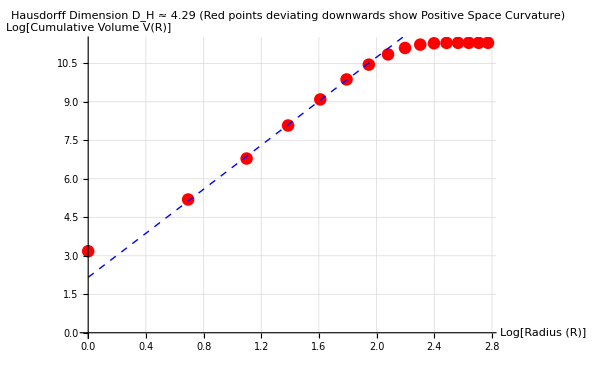

```mathematica
(* ====================================================*)(*【终极几何测量】:提取宏观豪斯多夫维度 (Hausdorff Dimension) 与曲率偏离*)(* ====================================================*)Print[Style["正在执行【宏观豪斯多夫维度】提取 (基于早期测地线体积增长)...",Blue,Bold]];

(*1. 从已有的 radiusData 中提取半径和对应的壳层节点数*)
radii=radiusData[[All,1]];
shellNodes=radiusData[[All,2]];

(*2. 计算累积体积 V(R) (即半径 R 内包罗的总节点数)*)
cumVolumes=Accumulate[shellNodes];

(*3. 清洗数据：剔除 R=0 的大爆炸奇点，防止 Log[0] 出现数学报错*)
validData=Select[Transpose[{radii,cumVolumes}],#[[1]]>0&];

(*4. 转换为双对数坐标 {Log[R],Log[V(R)]}*)
(*注意：这里用自然对数 Log 或者 常用对数 Log10 算出来的斜率是一模一样的*)
logData={Log[#[[1]]],Log[#[[2]]]}&/@validData;

(*5. 【核心步骤】截取平坦的线性起飞区 (我们取 R=2 到 R=6) 进行线性拟合*)
(*避开 R=1 的量子极早期波动，避开 R>7 的赤道严重弯曲*)
fitData=Select[logData,Log[2]<=#[[1]]<=Log[6]&];
fit=LinearModelFit[fitData,x,x];

(*6. 提取斜率，这就是内蕴的豪斯多夫维度 DH！*)
dH=fit["BestFitParameters"][[2]];
rSquared=fit["RSquared"];

Print[Style[StringForm["[测量结果] 宏观豪斯多夫维度 D_H = `` (拟合优度 R^2 = ``)",Round[dH,0.01],Round[rSquared,0.001]],Purple,Bold,16]];

(*7. 绘制终极对比图：完美平直时空 vs.真实的弯曲闭合时空*)
Print[Show[ListPlot[logData,PlotStyle->{Red,PointSize[0.015]},AxesLabel->{"Log[Radius (R)]","Log[Cumulative Volume V(R)]"},PlotLabel->Style[StringForm["Hausdorff Dimension \!\(\*SubscriptBox[\(D\), \(H\)]\) ≈ ``\n(Red points deviating downwards show Positive Space Curvature)",Round[dH,0.01]],14,Bold],ImageSize->600,GridLines->Automatic],(*画出代表平坦时空的理论延长线*)Plot[fit[x],{x,0,Log[16]},PlotStyle->{Blue,Dashed,Thick}]]]
```

```mathematica
1
```

1

```mathematica
1
```

1